```mathematica
Unprotect[Internal`EncodeCharacters];

Internal`EncodeCharacters[str_,enc_]:=Quiet[FromCharacterCode[ToCharacterCode[str],enc]]

SetDirectory[NotebookDirectory[]]
```

D:\Документы\Diploma_bac\PCA

```mathematica
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogPlot},PlotRange->Full,(*PlotRangePadding->{None,Automatic},*)Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier New",FontSize->12,Bold},ImageSize->500,PlotStyle->PointSize[0.01]];
```

```mathematica
sig1=Table[Sin[2 π *0.03* k]+Sin[2 π *0.036* k],{k,1,500}];
sig2=Table[0.8*(Sin[2 π *0.03* k+2π*0.15]+Sin[2 π *0.036* k+2π*0.15]),{k,1,500}];
sig3=Table[0.95*(Sin[2 π *0.03* k+2π*0.3]+Sin[2 π *0.036* k+2π*0.3]),{k,1,500}];
sig4=Table[0.85*(Sin[2 π *0.03* k+2π*0.45]+Sin[2 π *0.036* k+2π*0.45]),{k,1,500}];
```

```mathematica
SigM = Transpose[{{sig1},{sig2},{sig3},{sig4}}];
MatrixForm[SigM];
```

```mathematica
{u,w,v}=SVD=Chop[SingularValueDecomposition[SigM]];
```

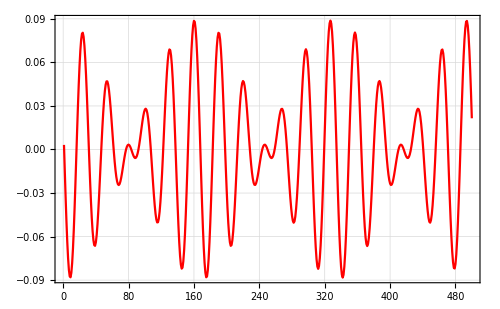

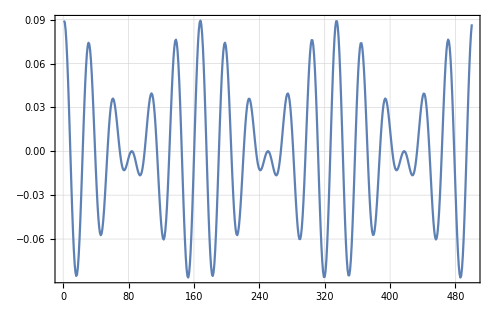

```mathematica
MatrixForm[w];
Ut1 = Transpose[v][[1]];
UT1=ListPlot[Ut1,Joined->True, PlotRange->All, PlotStyle->Red]
Ut2 = Transpose[v][[2]];
ListPlot[Ut2,Joined->True, PlotRange->All]
```

19

0.036

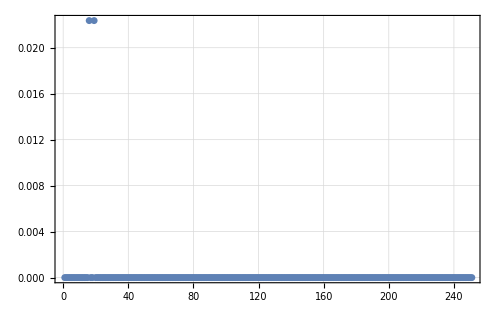

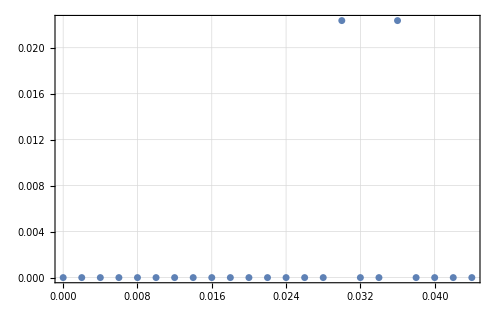

```mathematica
fsig=Fourier[Ut1,FourierParameters->{-1,1}];
fsig=Take[fsig,{1,Length[Ut1]/2+1}];
y=Abs[fsig];
maxY500=Max[y];
n=Position[y,maxY500][[1,1]]
len=Length[Ut1];
nu=Table[1.0*x/len,{x,0,len-1}];
nu500 = nu[[n]]
ListPlot[y,PlotRange->All]
ListPlot[Transpose[{nu[[1;;n+4]],y[[1;;n+4]]}],PlotRange->All]
```

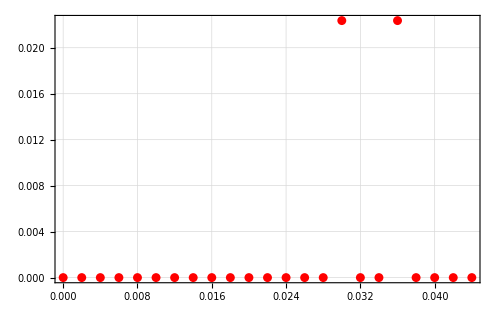

```mathematica
FUt1 = ListPlot[Transpose[{nu[[1;;n+4]],y[[1;;n+4]]}],PlotRange->All,PlotStyle->Red]
```

```mathematica
Ut2 = Transpose[SVD[[1;3]]][[2]];
ListPlot[Ut2,Joined->True, PlotRange->All]
```

-Graphics-

```mathematica
fsig=Fourier[Ut2,FourierParameters->{-1,-1}];
fsig=Take[fsig,{1,Length[Ut2]/2+1}];
y=Abs[fsig];
maxY500=Max[y];
n=Position[y,maxY500][[1,1]]
len=Length[Ut2];
nu=Table[1.0*x/len,{x,0,len-1}];
nu500 = nu[[n]]
ListPlot[y,PlotRange->All]
ListPlot[Transpose[{nu[[1;;n+4]],y[[1;;n+4]]}],PlotRange->All,PlotStyle->Red]
```

19

0.036

-Graphics-

-Graphics-

```mathematica
Export["Ut1.png",UT1]
Export["FUt1.png",FUt1]
```

Ut1.png

FUt1.png